## Undamped oscillator synthesis (Problem 3.20)

```mathematica
Clear["Global`*"];
tmax=7; tmaxu=7;ImpulseInput=DiracDelta[t];
G0=1/(s^2+1);  Dg=Denominator[G0];
```

First, the continuous case, using a modified PD control  [Example in text]

```mathematica
Ns1=n1+n2 s;  Ds1= d1+d2 s;  
Eq1=Together[Ns1 + Ds1 Dg- (s+3)^3];
K1=Ns1/Ds1/.SolveAlways[{Eq1==0},s] (* controller synth by pole placement *)
```

{(18+26 s)/(9+s)}

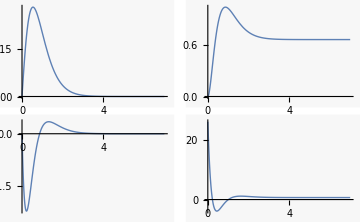

```mathematica
S1=Together[1/(1+K1 G0)]; T1=Together[1-S1];GS1=Together[G0 S1];
KS1=Together[K1 S1];

G0tf=TransferFunctionModel[G0,s] ;   (* continuous, stable osc. *)
T1tf=TransferFunctionModel[T1,s];
K1tf=TransferFunctionModel[K1,s];
GS1tf=TransferFunctionModel[GS1,s];  (* sys response to input disturbance *)
KS1tf=TransferFunctionModel[KS1,s];  (* sys response to input disturbance *) 

y0=OutputResponse[G0tf,ImpulseInput,{t,0,tmax}];   (* input to open-loop sys *)
y1=OutputResponse[GS1tf,ImpulseInput,{t,0,tmax}]; (* input disturb. *)
y1r=OutputResponse[T1tf,UnitStep[t],{t,0,tmax}];     (* sys to command step *)
u1=-OutputResponse[T1tf,ImpulseInput,{t,0,tmaxu}];   (* controller resp dist. *)
u1r=OutputResponse[KS1tf,UnitStep[t],{t,0,tmax}]; (* controller resp step *) 

py0=Plot[y0,{t,0,tmax}, PlotRange -> All];
py1=Plot[y1,{t,0,tmax}, PlotRange -> All];
py1r=Plot[y1r,{t,0,tmax}, PlotRange -> All];
pu1=Plot[u1,{t,0,tmaxu}, PlotRange -> All];
pu1r=Plot[u1r,{t,0,tmax}, PlotRange -> All]; 

GraphicsGrid[{{Show[py1],Show[py1r]},{Show[pu1],Show[pu1r]}},ImageSize->Medium]
```

Next, the continuous case, using a modified PID control [for corresponding problem]

```mathematica
Ns2=ki+kp s+kd s^2;  Ds2= s;  
Eq2=Together[Ns2 + Ds2 Dg- (s+3)^3];
K2=Ns2/Ds2/.SolveAlways[{Eq2==0},s](* controller synth by pole placement *)
```

{(27+26 s+9 s^2)/s}

NDSolve::irfail: Unable to reduce the index of the system to 0 or 1.

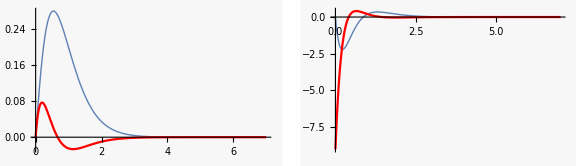

```mathematica
S2=Together[1/(1+K2 G0)]; T2=Together[1-S2];GS2=Together[G0 S2];
KS2=Together[K2 S2];

G2tf=TransferFunctionModel[G0,s] ;   (* continuous, stable osc. *)
T2tf=TransferFunctionModel[T2,s];
K2tf=TransferFunctionModel[K2,s];
GS2tf=TransferFunctionModel[GS2,s];  (* sys response to input disturbance *)
KS2tf=TransferFunctionModel[KS2,s];  (* sys response to input disturbance *)

y2=OutputResponse[GS2tf,ImpulseInput,{t,0,tmax}]; (* input disturb. *)
y2r=OutputResponse[T2tf,UnitStep[t],{t,0,tmax}];     (* sys to command step *)
u2=-OutputResponse[T2tf,ImpulseInput,{t,0,tmaxu}];   (* controller resp dist. *)
u2r=OutputResponse[KS2tf,UnitStep[t],{t,0,tmax}]; (* controller resp step *)

py2=Plot[y2,{t,0,tmax}, PlotRange -> All,PlotStyle->Red];
py2r=Plot[y2r,{t,0,tmax}, PlotRange -> All,PlotStyle->Red];
pu2=Plot[u2,{t,0,tmaxu}, PlotRange -> All,PlotStyle->Red];
pu2r=Plot[u2r,{t,0,tmax}, PlotRange -> All,PlotStyle->Red]; 

GraphicsRow[{Show[py1,py2],Show[pu1,pu2]},ImageSize->Large]
```

State-space representations for input-disturbance response:

```mathematica
{T1,T2}
```

{{(2 (9+13 s))/(3+s)^3},{(27+26 s+9 s^2)/(3+s)^3}}

```mathematica
{GS1ss=StateSpaceModel[GS1tf], T1ss=StateSpaceModel[T1tf]}
```

{01000010-27-27-919100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic,01000010-27-27-91182600StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic}

```mathematica
{GS2ss=StateSpaceModel[GS2tf], T1ss=StateSpaceModel[T2tf]}
```

{01000010-27-27-910100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic,01000010-27-27-91272690StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic}